### data reading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 , 0.0028 ,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
temperaturesG={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 , 0.0028 },{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
```

```mathematica
fitting={{FittedModel[0.23898763148144703 ⅇ^(-0.7211106123773332 t^0.9905357466803566)],FittedModel[0.22123964351289824 ⅇ^(-0.5081162986880765 t^0.9511396339070934)],FittedModel[0.1813696719780106 ⅇ^(-0.3507298388051473 t^0.9930494750768472)],FittedModel[0.16577791128195302 ⅇ^(-0.2912303418610043 t^0.9879292979090472)],FittedModel[0.14411751794695463 ⅇ^(-0.20788463714685138 t^0.9022831799281819)],FittedModel[0.09658280354484236 ⅇ^(-0.11581857257786517 t^0.8828882669751839)],FittedModel[0.08760721415971362 ⅇ^(-0.09637245640731837 t^0.8159026294982501)],FittedModel[0.07020110194421185 ⅇ^(-0.07511334107606668 t^0.8062337510106476)],FittedModel[0.05937561134616735 ⅇ^(-0.08317315106749175 t^0.6845737695316122)],FittedModel[0.048836380452269366 ⅇ^(-0.05075987031382538 t^0.6526187775027247)],FittedModel[0.03569699202636103 ⅇ^(-0.03166533694389245 t^0.6690148855945094)],FittedModel[0.03531848519915478 ⅇ^(-0.021074994886229558 t^0.6679971822938536)]},{FittedModel[0.210469118046167 ⅇ^(-0.7938673305375744 t^0.9970053134440804)],FittedModel[0.2002748961300614 ⅇ^(-0.5586240727804905 t^0.9813348589407216)],FittedModel[0.1806273537862311 ⅇ^(-0.4765595231428065 t^0.981078261470334)],FittedModel[0.10014608113788581 ⅇ^(-0.20232201307994113 t^0.9818746605677192)],FittedModel[0.07772934947715844 ⅇ^(-0.15394721380219303 t^0.9020537793550232)],FittedModel[0.06450524342378627 ⅇ^(-0.11782315045472638 t^0.9257557768211936)],FittedModel[0.05866414366896228 ⅇ^(-0.14134027263292148 t^0.8050483006655912)],FittedModel[0.047727724274976464 ⅇ^(-0.09356640760732075 t^0.8333036600243768)],FittedModel[0.03666066589187361 ⅇ^(-0.04938993543886252 t^0.915321448104085)],FittedModel[0.033797253182206444 ⅇ^(-0.0785185119281658 t^0.7432280394330144)],FittedModel[0.02949867341512681 ⅇ^(-0.11162507608036888 t^0.6279151641455616)],FittedModel[0.021193773072896997 ⅇ^(-0.03587731515162103 t^0.7888937213495182)],FittedModel[0.014743317364245908 ⅇ^(-0.03385560869970338 t^0.740276023641977)],FittedModel[0.011383487326596189 ⅇ^(-0.028682081067680207 t^0.639651869424772)]},{FittedModel[0.20799883964240143 ⅇ^(-0.8098184268914607 t^0.8354901079758212)],FittedModel[0.09401287222906148 ⅇ^(-0.29637945294085394 t^0.9275525318989086)],FittedModel[0.06313653974466157 ⅇ^(-0.18332252277836303 t^0.9439680250792427)],FittedModel[0.032683434191457084 ⅇ^(-0.08515922061763434 t^0.9711616582929677)],FittedModel[0.026236025213799096 ⅇ^(-0.07365365468953826 t^0.9148415158760231)],FittedModel[0.01917806521076566 ⅇ^(-0.06719555510866196 t^0.8488661795607308)],FittedModel[0.015066655548010347 ⅇ^(-0.03366425858030262 t^0.962263099308754)],FittedModel[0.009576548285157518 ⅇ^(-0.03450816470500544 t^0.796073568867949)],FittedModel[0.006344614093174089 ⅇ^(-0.0510752015177966 t^0.6280369262479917)],FittedModel[0.004242003291775964 ⅇ^(-0.03429485944928721 t^0.6423945269492174)],FittedModel[0.003308193342826314 ⅇ^(-0.031095739318193923 t^0.5823399541578139)],FittedModel[0.002484664423852477 ⅇ^(-0.0227353904306616 t^0.5710769222392241)],FittedModel[0.0019862087870626296 ⅇ^(-0.058420745418723295 t^0.4762657335117356)],FittedModel[0.0015874086983166163 ⅇ^(-0.04941404523698897 t^0.46712210614533833)],FittedModel[0.001506007590506098 ⅇ^(-0.042821039473438904 t^0.4917684765642241)],FittedModel[0.0015355849211028693 ⅇ^(-0.031965478941523136 t^0.47127628259879484)],FittedModel[0.0013497999360571802 ⅇ^(-0.049712807316666954 t^0.47276345232658007)]}};
```

```mathematica
tauAlphaCRSISF={{1.13.,2.12.,3.7.,5.24.,11.02.2,34.6.,58.10.,113.11.,234.7.,586.14.,1595.24.,2672.20.,4596.20.,8808.36.},{1.24.,2.4.,3.22.8,9.01.5,18.51.6,27.5.,41.5.,56.4.,95.5.,136.6.,227.11.,303.8.,563.9.,1171.15.,4893.45.,13252.74.},{1.42.6,4.71.5,8.91.7,20.91.5,28.01.5,48.4.,74.63.0,193.4.,557.10.,1213.42.,1624.29.,4184.45.,10376.187.,11687.237.,25941.343.,31903.490.,44031.615.}}
```

{{1.13.,2.12.,3.7.,5.24.,11.02.2,34.6.,58.10.,113.11.,234.7.,586.14.,1595.24.,2672.20.,4596.20.,8808.36.},{1.24.,2.4.,3.22.8,9.01.5,18.51.6,27.5.,41.5.,56.4.,95.5.,136.6.,227.11.,303.8.,563.9.,1171.15.,4893.45.,13252.74.},{1.42.6,4.71.5,8.91.7,20.91.5,28.01.5,48.4.,74.63.0,193.4.,557.10.,1213.42.,1624.29.,4184.45.,10376.187.,11687.237.,25941.343.,31903.490.,44031.615.}}

```mathematica
tauCRoverlap={{5.833319418117253,11.86278894161065,16.917338892978847,23.25548620200179,52.160702899712064,144.03673884723923,226.53383746332744,388.1550799983505,724.5750497347012,1566.498812260033,3781.0544591126413,5197.718904387892,9467.910598016313,16829.017670811918},{4.908732268246582,9.31848873794692,13.186591725727347,32.26259187830922,66.35481014996512,100.38226732553892,143.960577154809,209.23274864109732,333.8968037849868,460.04501744315485,668.6308529783303,958.8992763643564,1725.6436531887025,4336.275018528646,13857.138919303605,33009.675825311846},{7.834976775992932,22.460497359787702,40.922793734483406,94.78280185436874,128.79453931137476,231.55461796962314,323.17926259327726,843.8681996277791,2586.1167985909237,5036.916402039757,7314.717671434624,18600.880936529808,40307.93498223004,52624.590535830495,98462.79050610549,139254.67185534368,202268.02162912188}};
```

```mathematica
tauG={{1.520.20,2.020.11,2.90.4,3.460.27,5.00.6,10.90.5,18.30.5,25.30.5,44.41.3,118.83.4,196.12.2,349.6.},{1.260.22,2.00.4,2.40.6,5.10.4,6.81.3,8.80.7,11.32.5,17.80.7,25.61.6,34.72.1,45.42.4,71.12.4,90.5.,283.7.},{1.500.34,3.21.3,5.41.0,11.91.2,16.12.1,23.61.7,30.83.0,71.10.,160.19.,221.36.,390.67.,1489.261.,339.78.,588.144.,513.131.,1915.392.,551.181.}}
```

{{1.520.20,2.020.11,2.90.4,3.460.27,5.00.6,10.90.5,18.30.5,25.30.5,44.41.3,118.83.4,196.12.2,349.6.},{1.260.22,2.00.4,2.40.6,5.10.4,6.81.3,8.80.7,11.32.5,17.80.7,25.61.6,34.72.1,45.42.4,71.12.4,90.5.,283.7.},{1.500.34,3.21.3,5.41.0,11.91.2,16.12.1,23.61.7,30.83.0,71.10.,160.19.,221.36.,390.67.,1489.261.,339.78.,588.144.,513.131.,1915.392.,551.181.}}

```mathematica
plateauSISFfits={{0.2090.026,0.320.12,0.280.10,0.240.05,0.1610.015,0.10060.0035,0.08510.0016,0.06930.0010,0.05310.0011,0.04470.0006,0.032630.00026,0.032830.00033},{0.300.13,0.300.18,0.280.30,0.1320.024,0.0900.008,0.0730.005,0.0600.011,0.04650.0015,0.03790.0018,0.03100.0013,0.02420.0009,0.02050.0005,0.01500.0006,0.010490.00015},{0.170.04,0.0890.030,0.0670.012,0.03490.0031,0.02830.0030,0.01950.0010,0.01650.0014,0.00940.0010,0.00520.0004,0.00390.0004,0.002850.00020,0.001970.00015,0.002090.00022,0.001620.00017,0.001600.00018,0.001500.00012,0.001420.00020}};
```

```mathematica
tauBeta={{0.6642232137861881,0.8669948723116022,0.990530308188469,1.131667928812519,1.517021498828552,2.2323399454206005,2.5504192063135793,2.992492412019082,3.418883462627429,4.011490657756666,4.522430493882648,4.506816559609259,4.89872031328708,5},{0.6411469387095389,0.8369020714388854,0.9689226776978636,1.464292923930497,1.9892671465705398,2.429196655034924,2.850210048064606,3.344247063533591,3.9239172669212157,4.543217210696663,5.121882563594728,5.930253731457655,7.146032894282691,8.384680118171289,10.94432491600268,13.365128315693347},{0.5332092683108596,0.8838318278251224,1.1842198683893994,1.7648169650959271,2.1544346900318843,2.9644709215878033,3.477395801337251,5.25166517824382,8.145000008709289,10.913242242113366,12.632379043642509,20.389470170763463,32.04612907171944,38.0941323047135,57.5308764228518,80.22143549387202,107.48630541664379}};
```

### fit plateau

```mathematica
niceStretchedExp={{0,1,1,1,1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}};
```

```mathematica
niceStretchedExpStartEnd={{2,10},{2,14},{1,10}};
```

```mathematica
Gpfits=Table[NonlinearModelFit[Table[{temperatures[[p,T]],plateauSISFfits[[p,T]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],{A*x^B,{B<0.999}},{A,B},x],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[If[niceStretchedExp[[p,T]]==1,"ClosedMarkers","OpenMarkers"]
```

```mathematica
plateauSISFfits[[1,12,1]]
```

0.0328333

```mathematica
N[NumberForm[Gpfits[[3]]["BestFitParameters"][[2,2]],2]]
```

0.82

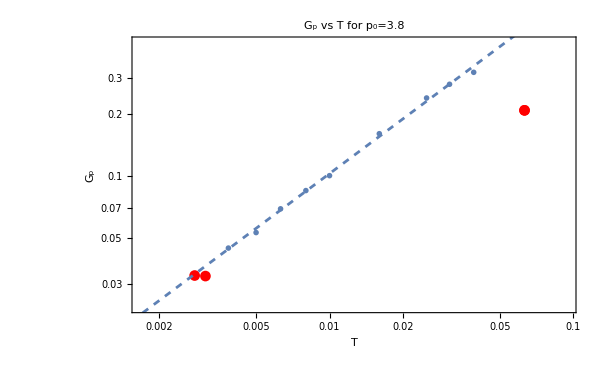
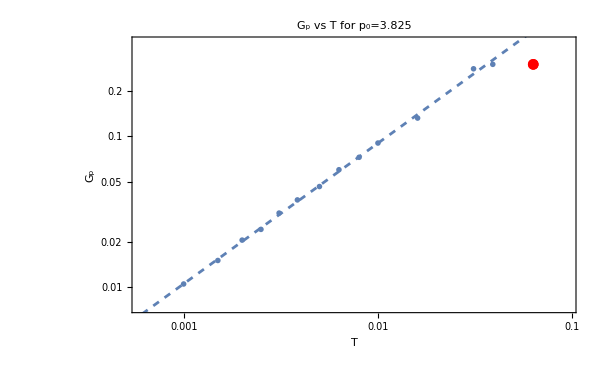
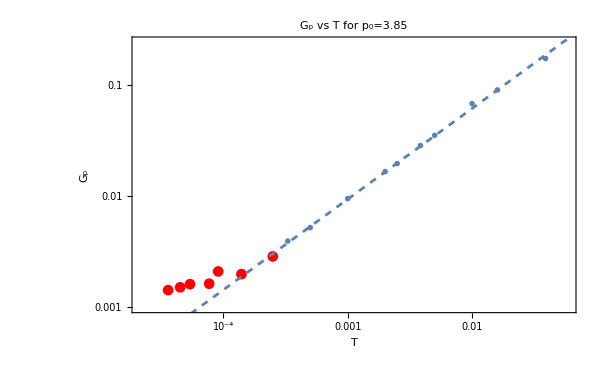

```mathematica
GpPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],plateauSISFfits[[p,T]][[1]]},{T,niceStretchedExpStartEnd[[p,1]]-1}],FrameLabel->{"T","G_p "},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"G_p vs T for p_0="<>ToString[p0s[[p]]],PlotRange->{{temperatures[[p,Length[temperaturesG[[p]]]]]*0.6,temperatures[[p,1]]*1.5},{plateauSISFfits[[p,Length[temperaturesG[[p]]]]][[1]]*0.7,Max[plateauSISFfits[[p,;;,1]]]*1.4}}],ListLogLogPlot[Table[{temperatures[[p,T]],plateauSISFfits[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],PlotLegends->"T^"<>ToString[NumberForm[Gpfits[[p]]["BestFitParameters"][[2,2]],2]],PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p "}],ListLogLogPlot[Table[{temperatures[[p,T]],plateauSISFfits[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperaturesG[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],LogLogPlot[Gpfits[[p]][T],{T,0.00001,0.1},PlotStyle->Dashed]],{p,1,3}]
```

```mathematica
Max[plateauSISFfits[[1,;;,1]]/temperatures[[1,;;]]]
```

11.7262

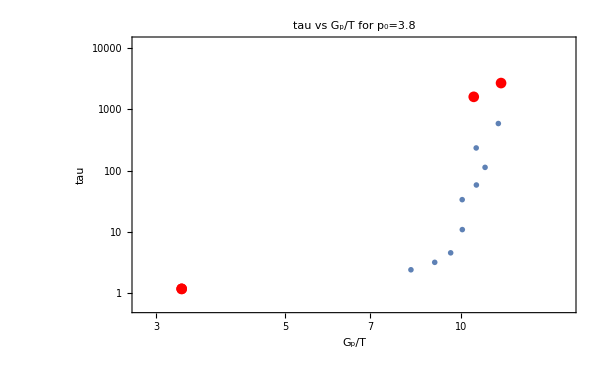
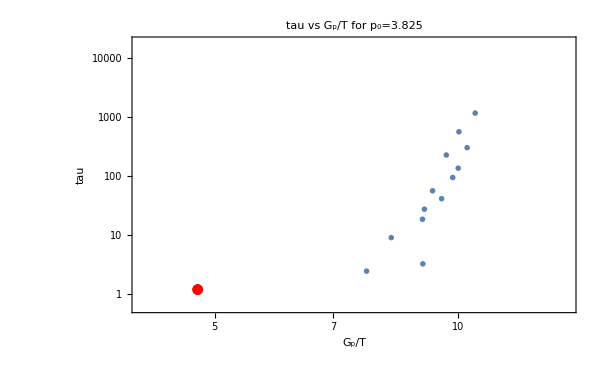
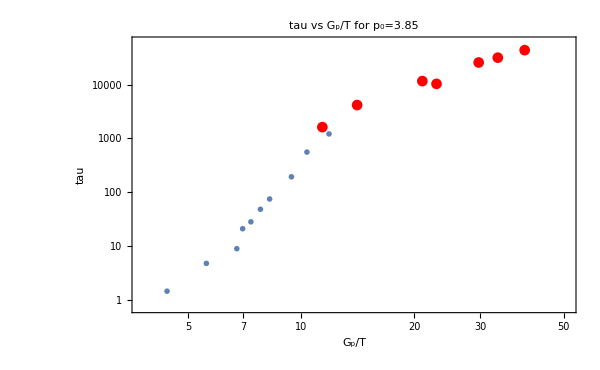

```mathematica
tauGpplots=Table[Show[ListLogLogPlot[Table[{plateauSISFfits[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]]-1}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T for p_0="<>ToString[p0s[[p]]],PlotRange->{{Min[plateauSISFfits[[p,;;,1]]/temperaturesG[[p,;;]]]*0.85,Max[plateauSISFfits[[p,;;,1]]/temperaturesG[[p,;;]]]*1.3},{Min[tauAlphaCRSISF[[p,;;,1]]]*0.5,Max[tauAlphaCRSISF[[p,;;,1]]]*1.4}}],ListLogLogPlot[Table[{plateauSISFfits[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p/T "}],ListLogLogPlot[Table[{plateauSISFfits[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperaturesG[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],LogLogPlot[Gpfits[[p]][T],{T,0.00001,0.1},PlotStyle->Dashed]],{p,Length[p0s]}]
```

```mathematica
tauAlphaNiceStretchedExpStartEnd={{2,7},{1,14},{2,10}};
```

```mathematica
tauAlphaCRSISF[[1,1,1]]
```

1.18553

```mathematica
taufitSISF=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],{A Exp[B t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{B,A},t,MaxIterations->10000],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
taufitSISF=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],{A Exp[B t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{B,A},t,MaxIterations->10000,Method->{"NMinimize","RandomSeed"->10000}],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],{A Exp[B t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{B,A},t,MaxIterations->10000],{p,1,1}]
```

{FittedModel[…]}

```mathematica
Simplify[Log[a b^0.5]]
```

Log[a b^0.5]

```mathematica
taufit[[1]]
```

Part::partd: Part specification taufit⟦1⟧ is longer than depth of object.

taufit⟦1⟧

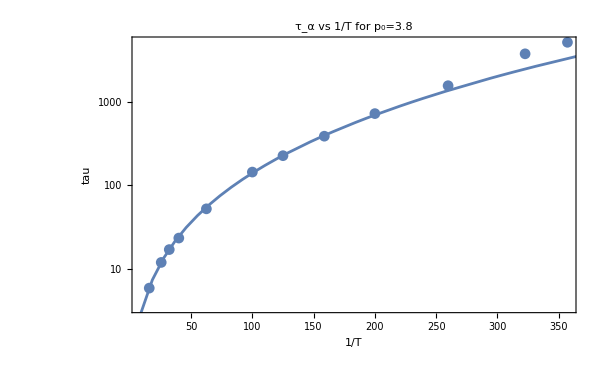

```mathematica
tauAlphaNiceStretchedExpStartEnd={{2,10},{1,14},{2,10}};
```

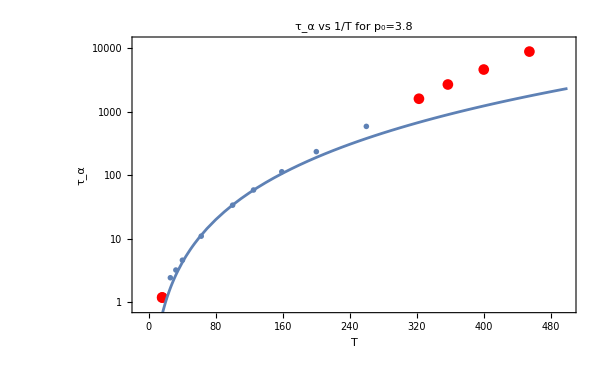
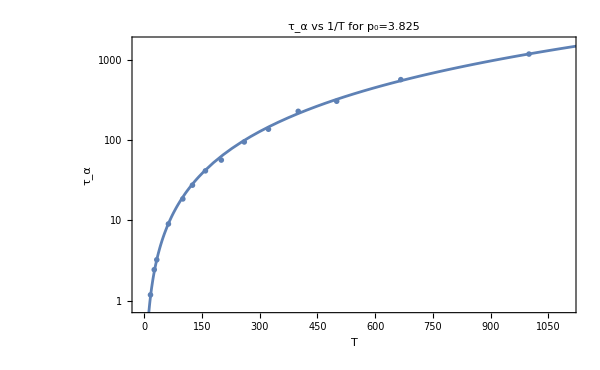
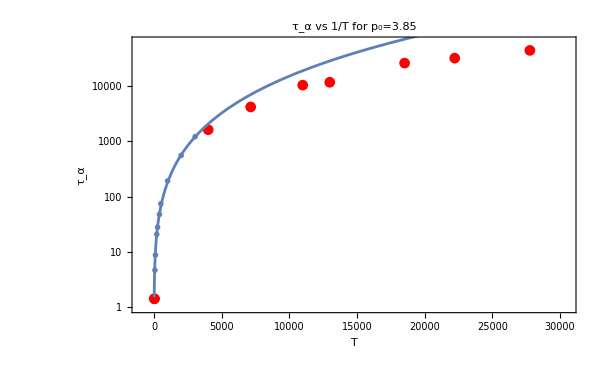

```mathematica
taufitPlots=Table[Show[ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T]][[1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]]-1}],FrameLabel->{"T","τ_α "},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->{{{-10,-10,-1000}[[p]],1/temperatures[[p,Length[temperatures[[p]]]]]*1.1},{tauAlphaCRSISF[[p,1]][[1]]*0.7,tauAlphaCRSISF[[p,Length[temperatures[[p]]],1]]*1.4}}],ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p "}],ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],LogPlot[taufitSISF[[p]][t],{t,10,{500,1200,30000}[[p]]}]],{p,Length[p0s]}]
```

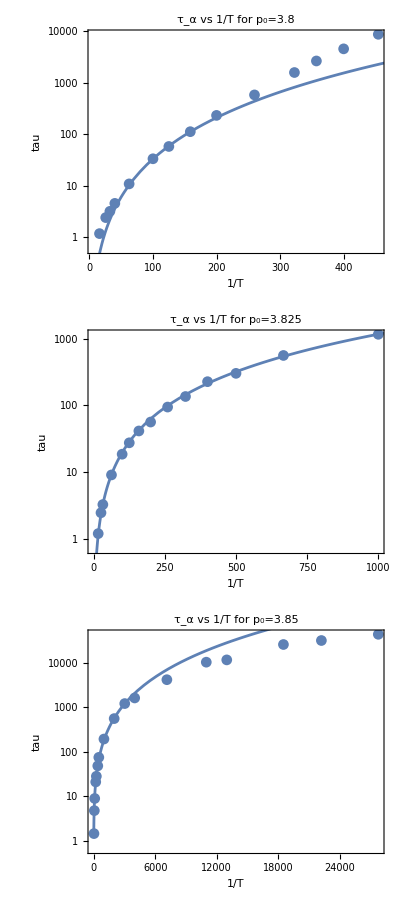

```mathematica
taufitPlots=Table[Show[ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","tau "},ImageSize->600,PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All(*PlotLegends->"Exp[T^-"<>ToString[NumberForm[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]],2]]<>"]"*)],LogPlot[taufitSISF[[p]][t],{t,10,{500,1200,30000}[[p]]}]],{p,1,3}];
Column[taufitPlots]
```

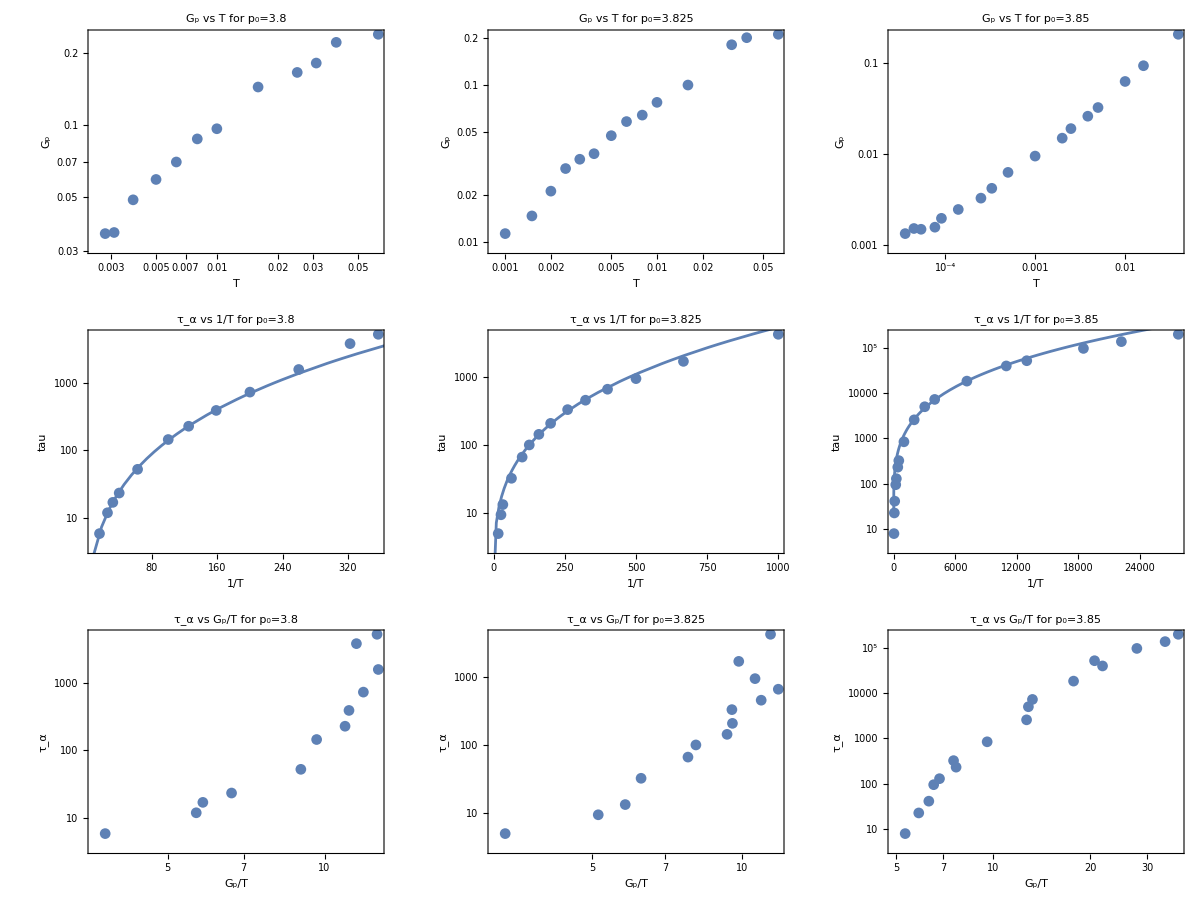

```mathematica
results=Grid[Partition[Flatten[{GPlots,taufitPlots,tauGpplots}],3]]
```

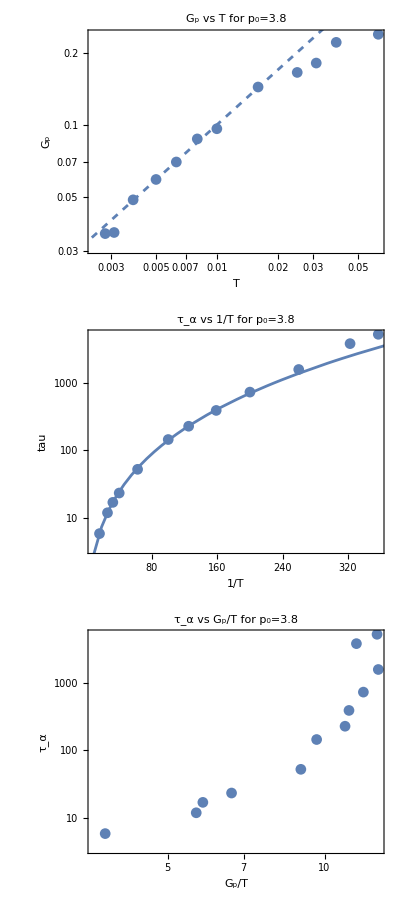

```mathematica
Column[{GPlots[[1]],taufitPlots[[1]],tauGpplots[[1]]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05312024/Gpresults"<>ToString[p0s[[p]]]<>".jpeg",Column[{GPlots[[p]],taufitPlots[[p]],tauGpplots[[p]]}],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05312024/Gpresults3.8.jpeg,/home/chengling/Research/updates/05312024/Gpresults3.825.jpeg,/home/chengling/Research/updates/05312024/Gpresults3.85.jpeg}

```mathematica
Export["/home/chengling/Research/updates/05312024/TauPLots.jpeg",Column[Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],tauAlphaCRSISF[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tauG[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","tau "},ImageSize->600,PlotLegends->{"CRSISF","CRoverlap","tau_G"},PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All(*PlotLegends->"Exp[T^-"<>ToString[NumberForm[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]],2]]<>"]"*)]],{p,1,3}]],ImageResolution->800]
```

/home/chengling/Research/updates/05312024/TauPLots.jpeg

## tauAlpha

```mathematica
tauG[[;;,;;,1]]
```

{{1.51817,2.02293,2.87152,3.45734,5.00091,10.9347,18.2796,25.3105,44.372,118.762,196.127,349.152},{1.26016,1.99363,2.40251,5.11629,6.79964,8.83772,11.2576,17.7547,25.6143,34.7176,45.3932,71.1069,90.0039,282.602},{1.49628,3.21946,5.35835,11.8582,16.0978,23.6207,30.8218,70.6446,160.5,220.531,390.16,1489.15,339.173,588.301,513.034,1914.79,550.834}}

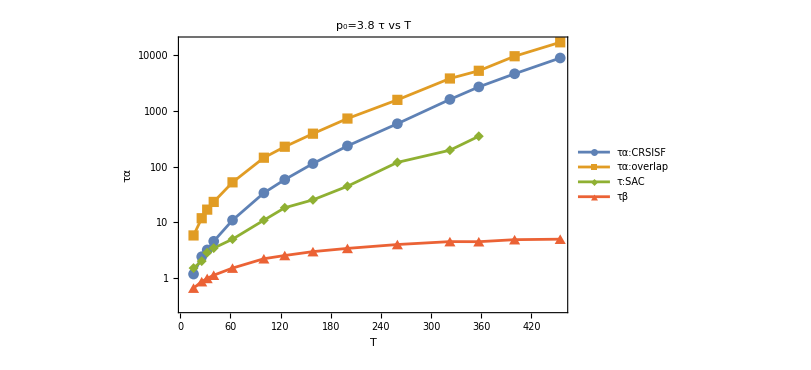
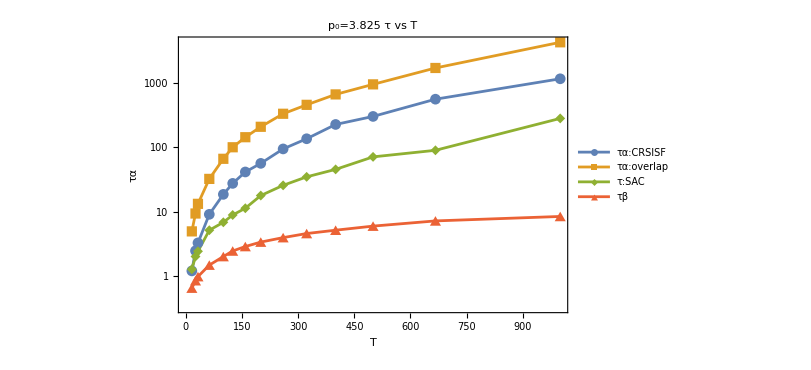
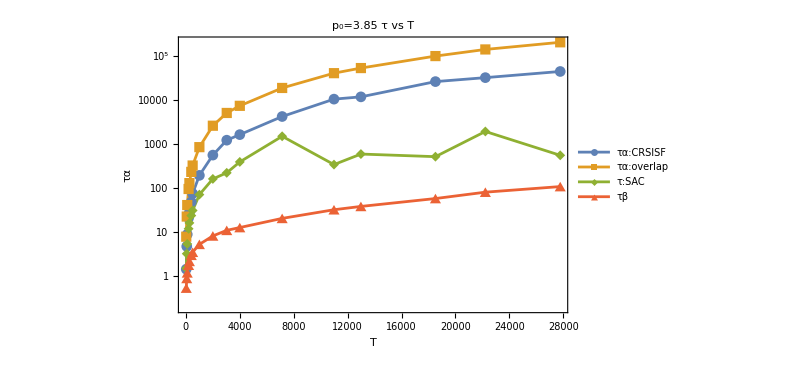

```mathematica
tauPlot=Table[ListLogPlot[{Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauG[[p,T,1]]},{T,Length[temperaturesG[[p]]]}],Table[{1/temperatures[[p,T]],tauBeta[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","τα"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" τ vs T",Joined->True,PlotRange->All,PlotLegends->{"τα:CRSISF","τα:overlap","τ:SAC","τβ"}],{p,Length[p0s]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/GpPlots"<>ToString[p0s[[p]]]<>".jpeg",GpPlots[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/GpPlots3.8.jpeg,/home/chengling/Research/updates/06242024/GpPlots3.825.jpeg,/home/chengling/Research/updates/06242024/GpPlots3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/tauGp"<>ToString[p0s[[p]]]<>".jpeg",tauGpplots[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/tauGp3.8.jpeg,/home/chengling/Research/updates/06242024/tauGp3.825.jpeg,/home/chengling/Research/updates/06242024/tauGp3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/tauFit"<>ToString[p0s[[p]]]<>".jpeg",taufitPlots[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/tauFit3.8.jpeg,/home/chengling/Research/updates/06242024/tauFit3.825.jpeg,/home/chengling/Research/updates/06242024/tauFit3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/taus"<>ToString[p0s[[p]]]<>".jpeg",tauPlot[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/taus3.8.jpeg,/home/chengling/Research/updates/06242024/taus3.825.jpeg,/home/chengling/Research/updates/06242024/taus3.85.jpeg}